#### Calculate expectation value of translation operator

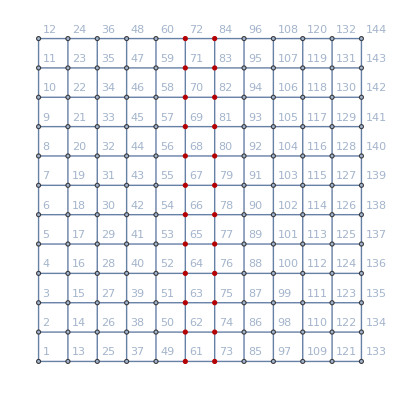

```mathematica
ClearAll["Global`*"]

n=12;(* Lx *)
n1=12;(* Ly *)
rightpt=1;(* Magnetic field upper bond *)
δ=0.03;(*chemical potential increment*)
div=0;(* div changes gauge origin, while fixing \delta=0 in Eq.(E2) *)
widthfromB=-1; (*width from bounday of partial translation, leave as -1 for full translation *)

add=2Pi/(n*n1)*numofflux;(*\phi*)
bdd=add*(n);

(*initialize graph*)
g=GridGraph[{n1,n}, VertexLabels->Automatic];

adj=AdjacencyMatrix[g];
zeros=Table[0,{i,Length[adj]},{j,Length[adj]}];
gaugechoice=zeros;
ones=Table[1,{i,Length[adj]},{j,Length[adj]}];


(* Define Ty as in Eq.(E2)), \delta is set to 0 *)

rpt4P=Flatten[Table[If[n/2-1/2+div-widthfromB <j<n/2-1/2+div+widthfromB,Nothing,{1+i+n1*j,1+Mod[i+1,n1]+n1*j}->1*E^(I*Which[j<n/2-1/2+div,-bdd/2,j>n/2-1/2+div,+bdd/2,j==n/2-1/2+div,0])],{i,0,n1-1},{j,0,n-1}]];
rpnm=Complement[VertexList[g],Flatten[Table[If[n/2-1/2+div-widthfromB <j<n/2-1/2+div+widthfromB,Nothing,1+i+n1*j],{i,0,n1-1},{j,0,n-1}]]];
HighlightGraph[g,rpnm](*Highlights the region that is not translated *)

rpNM=Table[{rpnm[[i]],rpnm[[i]]}->1,{i,Length[rpnm]}];

ty=ReplacePart[zeros,rpt4P];
ty=ReplacePart[ty,rpNM];
ty=SparseArray[ty];

(* Hamiltonian *)

path=Table[FindShortestPath[g,i,i+n*n1-n1],{i,1,n1}];
path2=Table[FindShortestPath[g,1+n1*i,n1+n1*i],{i,0,n-1}];

(*connecting boundaries*)
replace=Flatten[Table[{(path[[i,j]]),(path[[i,Mod[j+1,n1,1]]])}->1,{i,Length[path]},{j,Length[path[[i]]]}]];
replace2=Flatten[Table[{(path[[i,Mod[j+1,n1,1]]]),(path[[i,j]])}->1,{i,Length[path]},{j,Length[path[[i]]]}]];
replace3=Flatten[Table[{(path2[[i,j]]),(path2[[i,Mod[j+1,n,1]]])}->1,{i,Length[path2]},{j,Length[path2[[i]]]}]];
replace4=Flatten[Table[{(path2[[i,Mod[j+1,n,1]]]),(path2[[i,j]])}->1,{i,Length[path2]},{j,Length[path2[[i]]]}]];

disLH=adj;

disLH=ReplacePart[disLH,replace];
disLH=ReplacePart[disLH,replace2];
disLH=ReplacePart[disLH,replace3]; 
disLH=ReplacePart[disLH,replace4];

(* define vector potential *)

(*gauge origin \bar{o}_x is automatically set to Lx/2, i.e. plaquette center if Lx even, vertex center if Lx odd *)
addlist=Flatten[Table[{(path2[[i,j]]),(path2[[i,Mod[j+1,n1,1]]])}->-(i-n/2-0.5-div)*add*I,{i,Length[path2]},{j,Length[path2[[i]]]}]];

bddlist=Flatten[Table[{(path[[i,-1]]),(path[[i,1]])}->(i-n1/2)*bdd*I,{i,Length[path]}]];

addmat=ReplacePart[zeros,addlist];
bddmat=ReplacePart[zeros,bddlist];

gaugechoice+=addmat;
gaugechoice+=bddmat;

gaugechoice+=ConjugateTranspose[gaugechoice];

disLH=-Table[disLH[[i,j]]*Exp[gaugechoice[[i,j]]],{i,Length[adj]},{j,Length[adj]}];


slaterCon[psi1_,psi2_]:=If[psi1=={}||psi2=={},1,Det[Table[Conjugate[psi1[[i]]].psi2[[j]],{i,Length[psi1]},{j,Length[psi2]}]]];

savedlowerband={};
savedphase=0;

(* iterate over magnetic field *)
chargeTab=ParallelTable[

numofflux=iterA;
{val1,vec1}=Eigensystem[Normal[disLH]/.numofflux->iterA];
eigen={val1,vec1};

(* iterate over chemical potential *)
phaseoutput=Table[

lowerbandid=Position[val1,n_ /;-4<n<=iterB]//Flatten;

lowerband=Join[Table[vec1[[lowerbandid[[i]]]] ,{i,Length[lowerbandid]}]];
If[lowerband!=savedlowerband,
phase1=TimeConstrained[Arg[slaterCon[If[lowerband=={},{},lowerband.ty],lowerband]]/(2Pi),20,1];
(*phase1=TimeConstrained[Arg[slaterCon[lowerband,If[lowerband=={},{},Transpose[ty.Transpose[lowerband]]]]]/(2Pi),20,1];*)
savedphase=phase1;
,
phase1=savedphase;
];
savedlowerband=lowerband;
phase1

,{iterB,-4,4,δ}]

,{iterA,1,(n*n1)*rightpt,1},Method->"FinestGrained"];
```

#### plotting

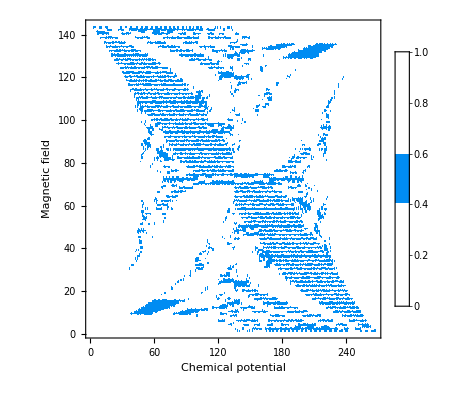

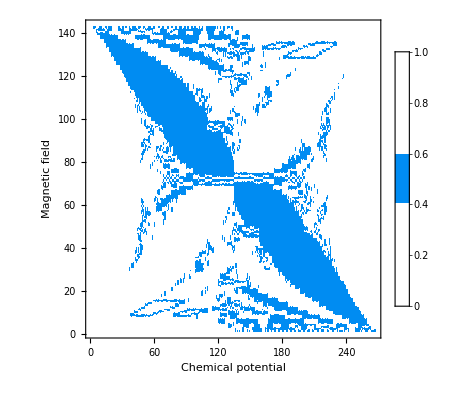

```mathematica
fracC1=Mod[N[chargeTab],1]//Chop;
difrac=Mod[Drop[fracC1,1]-Drop[fracC1,-1],1];

ListDensityPlot[fracC1,ColorFunction->Function[z,If[0.4<z<0.6,RGBColor[0., 0.55, 0.95],White]],PlotLegends->Automatic,FrameLabel->{"Chemical potential","Magnetic field"},InterpolationOrder->0]
ListDensityPlot[difrac,ColorFunction->Function[z,If[0.4<z<0.6,RGBColor[0., 0.55, 0.95],White]],PlotLegends->Automatic,FrameLabel->{"Chemical potential","Magnetic field"},InterpolationOrder->0]
```